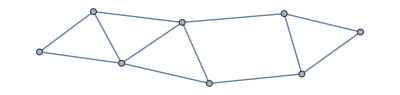

```mathematica
weightedUndirectedGraph = Graph[{a<-> b,a<->c,b<->c,b<->d,c<->e, c <-> d, d <->e, d<->f, e<-> g, f <->g, f<->z, g<->z}, EdgeWeight->{4,3,2,5,6,3,1,5,5,2,7,4}]
```

```mathematica
FindShortestPath[weightedUndirectedGraph, a,z]
```

{a,c,d,e,g,z}

```mathematica
ac=3
cd=3
de = 1
eg= 5
gz = 4
ac + cd + de + eg +gz
```

3

3

1

5

4

16